```mathematica
d=0.12; t=0.4; c=6.25;a1=0.016; G1=0.00086; b=0.0004138; mu1=0.13;
f4[x_,n1_,U_]:=√(U^2+(a1*n1/x)+t^2/2-√((t^2+4*U^2)*(a1*n1/x)+t^4/4));
f4[0.1,1,0.1];
F2[x_,n1_,U_]=(1/((mu1-f4[x,n1,U])^2+G1^2));
F1[x_,U_]=b*G1*Sum[F2[x,n1,U],{n1,0,100}]*(1/x);
F1[0.1,1]
```

0.0030673

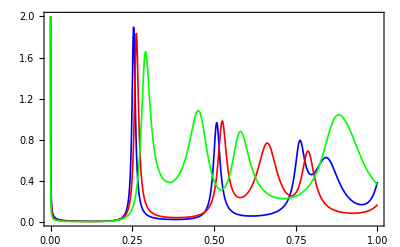

```mathematica
Plot[{F1[x,0.155],F1[x,0.160],F1[x,0.168]},{x,0,1},PlotRange->{0,2},PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Red},{Thickness[0.003],Green}},Frame->True]
```

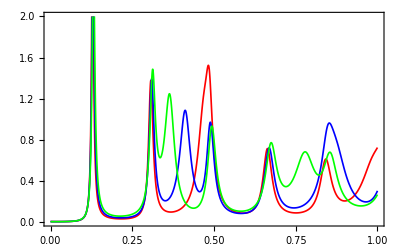

```mathematica
d=0.12; mu2=0.225;
f5[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2/2-√((t^2+4*U^2)*(a1*n1/x)+4*U^2*d^2+2*t^2*d*U+t^4/4));
F3[x_,n1_,U_]=(1/((mu2-f5[x,n1,U])^2+G1^2));
F4[x_,U_]=b*G1*Sum[F3[x,n1,U],{n1,0,100}]*(1/x);
Plot[{F4[x+0.05,-0.155],F4[x+0.05,-0.160],F4[x+0.05,-0.165]},{x,0,1},PlotRange->{0,2},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Green}},Frame->True]
```

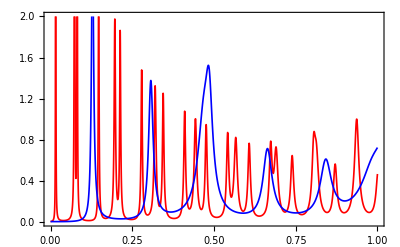

```mathematica
d=0.12; mu3=0.13;
f6[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2-2*√((t^2+U^2)*(a1*n1/x)+U^2*d^2));
F5[x_,n1_,U_]=(1/((mu3-f6[x,n1,U])^2+G1^2));
F6[x_,U_]=b*G1*Sum[F5[x,n1,U],{n1,0,100}]*(1/x);
Plot[{F6[x+0.05,-0.155],F4[x+0.05,-0.155]},{x,0,1},PlotRange->{0,2},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue}},Frame->True]
```